```mathematica
FourierBSCall[S_,K_,tau_,r_,d_,V_,n_]:=Module[{X=Log[S/K]+(r-d) tau},
S Exp[-d tau]-K Exp[-r tau]/Pi*
Re[ CoeffBasedIntegrate[(Exp[-X I( #+I/2) -(#^2+1/4)/2 V ]/
(#^2+1/4))& ,RiemanCoeffs[n,0,15]]]]
```

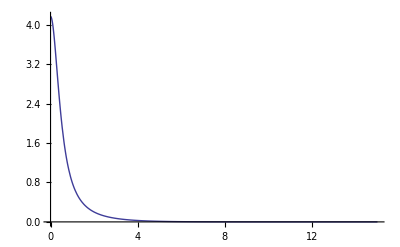

```mathematica
S=100;K=90;tau=1.;r=0.0;d=0;
V=0.09;
Plot[Re[(Exp[-Log[S/K]I( k+I/2) -(k^2+1/4)/2 V ]/
(k^2+1/4))],{k,0,15},PlotRange->All]
```

```mathematica
N[RiemanCoeffs[50,0,15]]
```

{{0.,0.15},{0.3,0.3},{0.6,0.3},{0.9,0.3},{1.2,0.3},{1.5,0.3},{1.8,0.3},{2.1,0.3},{2.4,0.3},{2.7,0.3},{3.,0.3},{3.3,0.3},{3.6,0.3},{3.9,0.3},{4.2,0.3},{4.5,0.3},{4.8,0.3},{5.1,0.3},{5.4,0.3},{5.7,0.3},{6.,0.3},{6.3,0.3},{6.6,0.3},{6.9,0.3},{7.2,0.3},{7.5,0.3},{7.8,0.3},{8.1,0.3},{8.4,0.3},{8.7,0.3},{9.,0.3},{9.3,0.3},{9.6,0.3},{9.9,0.3},{10.2,0.3},{10.5,0.3},{10.8,0.3},{11.1,0.3},{11.4,0.3},{11.7,0.3},{12.,0.3},{12.3,0.3},{12.6,0.3},{12.9,0.3},{13.2,0.3},{13.5,0.3},{13.8,0.3},{14.1,0.3},{14.4,0.3},{14.7,0.3},{15.,0.15}}

```mathematica
S=100;K=90;tau=1.;r=0.0;d=0;
V=0.09;
FourierBSCall[S,K,tau,r,d,V,50]
```

17.0075

```mathematica
S=100;K=90;tau=1.;r=0.0;d=0;
V=0.09;
BS[S,K,tau,√V]
```

17.0129